```mathematica
Clear["Global`*"]
$MinPrecision=16;
precision=16;
```

```mathematica
(* Functions to form Butcher matrices/vectors given coefficients. S# stands for #-order SDIRK, where the diagonal entry is given first in the parameters, and D# stands for #-order DIRK. *)
S1[ad_]:={{ad}};
S2[ad_,a21_] :={{ad,0},{a21,ad}};
D2[a11_,a21_,a22_] :={{a11,0},{a21,a22}};
S3[ad_,a21_,a31_,a32_] :={{ad,0,0},{a21,ad,0},{a31,a32,ad}};
D3[a11_,a21_,a22_,a31_,a32_,a33_] :={{a11,0,0},{a21,a22,0},{a31,a32,a33}};
S4[ad_,a21_,a31_,a32_,a41_,a42_,a43_] :={{ad,0,0,0},{a21,ad,0,0},{a31,a32,ad,0},{a41,a42,a43,ad}};
D4[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_] :={{a11,0,0,0},{a21,a22,0,0},{a31,a32,a33,0},{a41,a42,a43,a44}};
S5[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{ad,0,0,0,0},{a21,ad,0,0,0},{a31,a32,ad,0,0},{a41,a42,a43,ad,0},{a51,a52,a53,a54,ad}};
D5[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_] :={{a11,0,0,0,0},{a21,a22,0,0,0},{a31,a32,a33,0,0},{a41,a42,a43,a44,0},{a51,a52,a53,a54,a55}};
S6[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{ad,0,0,0,0,0},{a21,ad,0,0,0,0},{a31,a32,ad,0,0,0},{a41,a42,a43,ad,0,0},{a51,a52,a53,a54,ad,0},{a61,a62,a63,a64,a65,ad}};
D6[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_,a61_,a62_,a63_,a64_,a65_,a66_] :={{a11,0,0,0,0,0},{a21,a22,0,0,0,0},{a31,a32,a33,0,0,0},{a41,a42,a43,a44,0,0},{a51,a52,a53,a54,a55,0},{a61,a62,a63,a64,a65,a66}};
E1:={{0.0}};
E2[a21_] :={{0,0},{a21,0}};
E3[a21_,a31_,a32_] :={{0,0,0},{a21,0,0},{a31,a32,0}};
E4[a21_,a31_,a32_,a41_,a42_,a43_] :={{0,0,0,0},{a21,0,0,0},{a31,a32,0,0},{a41,a42,a43,0}};
E5[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{0,0,0,0,0},{a21,0,0,0,0},{a31,a32,0,0,0},{a41,a42,a43,0,0},{a51,a52,a53,a54,0}};
E6[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{0,0,0,0,0,0},{a21,0,0,0,0,0},{a31,a32,0,0,0,0},{a41,a42,a43,0,0,0},{a51,a52,a53,a54,0,0},{a61,a62,a63,a64,a65,0}};
b1[bb1_]:={{bb1}};
b2[bb1_,bb2_]:={{bb1,bb2}};
b3[bb1_,bb2_,bb3_]:={{bb1,bb2,bb3}};
b4[bb1_,bb2_,bb3_,bb4_]:={{bb1,bb2,bb3,bb4}};
b5[bb1_,bb2_,bb3_,bb4_,bb5_]:={{bb1,bb2,bb3,bb4,bb5}};
b6[bb1_,bb2_,bb3_,bb4_,bb5_,bb6_]:={{bb1,bb2,bb3,bb4,bb5,bb6}};

(* Function to select Runge-Kutta Scheme and build Butcher Tableaux *)
GetButcher[type_,p_,stable_,s_,ver_]:= (
Which[type=="SDIRK" && p==1, (
(* A/L-stable, p=1, s=1 (Backward Euler) *)
A0 = S1[1.0];
b0 = b1[1.0]; ),
(* SDIRK L-stable, p=2, s=2 *)
type=="SDIRK" && stable=="L" && p==2, (
gamma=1.0-1.0/Sqrt[2.0];
A0 = S2[gamma,1.0-gamma];
b0=b2[1.0-gamma,gamma]; ),
(* SDIRK L-stable, p=3, s=3 *)
type=="SDIRK" && stable=="L" && p==3, (
q=0.435866521508458999416019;
r=1.20849664917601007033648;
z=0.717933260754229499708010;
A0 = S3[q,z-q,r,1.0-q-r];
b0=b3[r,1.0-q-r,q]; ),
(* SDIRK L-stable, p=4, s=5 *)
type=="SDIRK" && stable=="L" && p==4,(
A0=S5[0.25,0.5,17.0/50.0,-1.0/25.0,371.0/1360.0,-137.0/2720.0,15.0/544.0,25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0];
b0=b5[25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0,0.25]; ),

(* SDIRK A-stable, p=2, s=1 *)
type=="SDIRK" && stable=="A" && p==2, (
A0 = S1[0.5];
b0=b1[1.0]; ),
(* SDIRK A-stable, p=3, s=2 - Carpenter (223) *)
type=="SDIRK" && stable=="A" && p==3,(
g=(3.0+Sqrt[3.0])/6.0;
A0 = S2[g,1.0-2.0*g];
b0=b2[0.5,0.5]; ),
(* SDIRK A-stable, p=4, s=3 - Carpenter (232) *)
type=="SDIRK" && stable=="A" && p==4,(
q=1.0/Sqrt[3.0]*Cos[Pi/18.0]+0.5;
r=1.0/(6.0*(2.0*q-1.0)*(2.0*q-1.0));
A0=S3[q,0.5-q,2.0*q,1.0-4.0];
b0=b3[r,1.0-2.0*r,r]; ),


(* ESDIRK A-stable, p=2, s=2 (trap rule) *)
type=="ESDIRK" && stable=="A" && p==2, (
A0 = D2[0.0,0.5,0.5];
b0=b2[0.5,0.5]; ),
(* ESDIRK L-stable, p=2, s=3 - Carpenter 4.1.1 *)
type=="ESDIRK" && stable=="L" && p==2 , (
gamma=(2.0 - Sqrt[2.0])/2.0;
q2 = (1−2.0*gamma)/(4.0*gamma);
A0=D3[0.0,gamma,gamma,1-q2-gamma,q2,gamma];
b0=b3[1-q2-gamma,q2,gamma];
),
(* ESDIRK A-stable, p=3, s=3 - Carpenter 4.2.1 *)
type=="ESDIRK" && stable=="A" && p==3 && s==3, (
gamma=(3.0 + Sqrt[3.0])/6.0;
c3=1.0;    (*Stiffly accurate, A-stable*)
a32=c3*(c3-2*gamma)/(4.0*gamma);
q2=(3.0*c3-2.0)/(12*gamma*(c3-2*gamma));
q3=(1.0-3*gamma)/(3*c3*(c3-2*gamma));
A0=D3[0.0,gamma,gamma,c3-a32-gamma,a32,gamma];
b0=b3[1-q2-q3,q2,q3];
),

(* Gauss- methods *)
qgauss[n_,x_]:=D[x^n*(x-1)^n,{x,n}];
	cgauss[n_]:=(x/.NSolve[qgauss[n,x]==0,x,WorkingPrecision->precision])//Re//(Sort[#,Less]&);
	lgauss[n_,k_,x_]:=qgauss[n,x]/((x-cgauss[n][[k]]) (D[qgauss[n,x],x]/.x->cgauss[n][[k]]));
	agauss[n_,i_,k_]:=NIntegrate[lgauss[n,k,x],{x,0,cgauss[n][[i]]},WorkingPrecision->precision];
bgauss[n_,i_]:=NIntegrate[lgauss[n,i,x],{x,0,1},WorkingPrecision->precision];
	AG[n_]:=Table[agauss[n,i,k],{i,1,n},{k,1,n}];
bG[n_] := Table[bgauss[n,i],{i,1,n}];
cG[n_]:=cgauss[n];
type == "Gauss" && p==4, (
A0 = {{1/4.0,1/4.0-Sqrt[3.0]/6},{1/4.0+Sqrt[3.0]/6,1/4.0}};
b0 = b2[0.5,0.5];
),
type == "Gauss" && p==6, (
A0 = {{5.0/36.0,2.0/9-Sqrt[15.0]/15,5.0/36-Sqrt[15.0]/30},{5.0/36+Sqrt[15.0]/24,2.0/9,5.0/36-Sqrt[15.0]/24},{5.0/36+Sqrt[15.0]/30,2.0/+Sqrt[15.0]/15,5.0/36.0}};
b0 = b3[5.0/18.0,4.0/9.0,5.0/18.0];
),
type == "Gauss" && p==8, (
A0 = AG[4];
b0 = bG[4];
),
type == "Gauss" && p==10, (
A0 = AG[5];
b0 = bG[5];
),

(* Lobatto IIIA methods (A-stable) *)
type=="Lob3A" && p==2, (
A0={{0,0},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3A" && p==4, (
A0={{0,0,0},{5.0/24,1.0/3,-1.0/24},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIB methods (A-stable) *)
type=="Lob3B" && p==2, (
A0={{0.5,0},{0.5,0}};
b0=b2[0.5,0.5];
),
type=="Lob3B" && p==4, (
A0={{1.0/6.0,-1.0/6,0},{1.0/6,1.0/3,0},{1.0/6,5.0/6,0}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIC methods (L-stable) *)
type=="Lob3C" && p==2, (
A0={{0.5,-0.5},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3C" && p==4, (
A0={{1.0/6.0,-1.0/3,1.0/6},{1.0/6,5.0/12,-1.0/12},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
type=="Lob3C" && p==6, (
A0={{1.0/12,-Sqrt[5.0]/12,Sqrt[5.0]/12,-1.0/12},{1.0/12,1.0/4,(10-7*Sqrt[5.0])/60,Sqrt[5.0]/60},{1.0/12,(10+7*Sqrt[5.0])/60,1.0/4,-Sqrt[5.0]/60},{1.0/12,5.0/12,5.0/12,1.0/12}};
b0=b4[1.0/12,5.0/12,5.0/12,1.0/12];
),
(* Lobatto IIID methods (L-stable) This may night be right? *)
type=="Lob3D" && p==2, (
A0={{0.5,0.5},{-0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3D" && p==4, (
A0={{1.0/6.0,0,-1.0/6},{1.0/12,5.0/12,0},{1.0/2,1.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Radau 2A methods (L-stable)*)
qrad[n_,x_]:=LegendreP[n,2*x-1]-LegendreP[n-1,2*x-1];
crad[n_]:=(x/.NSolve[qrad[n,x]==0,x, WorkingPrecision->precision])//Re //(Sort[#,Less]&);
lrad[n_,k_,x_] :=qrad[n,x]/((x-crad[n][[k]]) (D[qrad[n,x],x]/.x->crad[n][[k]]));
arad[n_,i_,k_]:= NIntegrate[lrad[n,k,x],{x,0,crad[n][[i]]}, WorkingPrecision->precision];
AR[n_]:=Table[arad[n,i,k],{i,1,n},{k,1,n}];

type == "Radau" && p == 3, (
A0 = {{5.0/12,-1.0/12},{3.0/4,1.0/4}};
b0 = b2[3.0/4,1.0/4];
),
type == "Radau" && p == 5, (
A0 = {{11.0/45-7*Sqrt[6.0]/360, 37.0/225 - 169*Sqrt[6.0]/1800,-2.0/225+Sqrt[6.0]/75},{37.0/225+169*Sqrt[6.0]/1800, 11.0/45+7*Sqrt[6.0]/360,-2.0/225-Sqrt[6.0]/75},{4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9}};
b0 = b3[4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9];
),
type == "Radau" && p == 7, (
A0 = AR[4];
b0 = b4[A0[[4,1]],A0[[4,2]],A0[[4,3]],A0[[4,4]]];
),
type == "Radau" && p == 9, (
A0 = AR[5];
b0 = b5[A0[[5,1]],A0[[5,2]],A0[[5,3]],A0[[5,4]],A0[[5,5]]];
),
type == "Radau" && p == 11, (
A0 = AR[6];
b0 =b6[A0[[6,1]],A0[[6,2]],A0[[6,3]],A0[[6,4]],A0[[6,5]],A0[[6,6]]];
),

(* ERK, p=1 (forward Euler) *)
type=="ERK" && p==1,(
A0={{0.0}};
b0=b1[1.0]; ),
(* ERK, p=2 *)
type=="ERK" && p==2,(
A0=E2[1.0];
b0=b2[0.5,0.5]; ),
(* ERK, p=3 *)
type=="ERK" && p==3,(
A0=E3[0.5,-1.0,2.0];
b0=b3[1.0/6.0,2.0/3.0,1.0/6.0]; ),
(* ERK, p=4 *)
type=="ERK" && p==4, (
A0=E4[0.5,0.0,0.5,0.0,0.0,1.0];
b0=b4[1.0/6.0,1.0/3.0,1.0/3.0,1.0/6.0]; ),
(* ERK, p=5, v1 *)
type=="ERK" && p==5 && ver==1, (
A0=E6[0.25,0.125,0.125,0,0,0.5,3.0/16.0,-0.375,0.375,9.0/16.0,-3.0/7.0,8.0/7.0,6.0/7.0,-12.0/7.0,8.0/7.0];
b0=b6[7.0/90.0,0.0,16.0/45.0,2.0/15.0,16.0/45.0,7.0/90.0]; ),
(* ERK, p=5, v2 *)
type=="ERK" && p==5 && ver==2, (
A0=E6[1.0/3.0,4.0/25.0,6.0/25.0,1.0/4.0,-3.0,15.0/4.0,2.0/27.0,10.0/9.0,-50.0/81.0,8.0/81.0,2.0/25.0,12.0/25.0,2.0/15.0,8.0/75.0,0.0];
b0=b6[23.0/192.0,0.0,125.0/192.0,0.0,-27.0/64.0,125.0/192.0]; )
];
Return [{A0,b0}];
);

(* Functions to compute lambda^k and mu^k as a function of A, k, and dt*xi, for spatial eigenvaue xi *)
lambdak[x_,k_,A_,b_]:=(1.0-x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]]^k;
mu[x_,k_,A_,b_]:=1.0-(k*x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+k*x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]];
phiF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFCF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFn[x_,k_,A_,b_,c_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFCFn[x_,k_,A_,b_,nc_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
phiFCFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]]*Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
exact[x_,k_]:=Exp[-x*k];
prec[x_,Af_,Ac_]:=Abs[Eigenvalues[Inverse[IdentityMatrix[Dimensions[Ac][[1]]]+x*Ac].(IdentityMatrix[Dimensions[Af][[1]]]+x*Af)]];

linethick=0.0035;
fontsize=14;
```

(0.196815 | -0.0655354 | 0.023771
0.394424 | 0.292073 | -0.0415488
0.376403 | 0.512486 | 0.111111)

(1.)

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

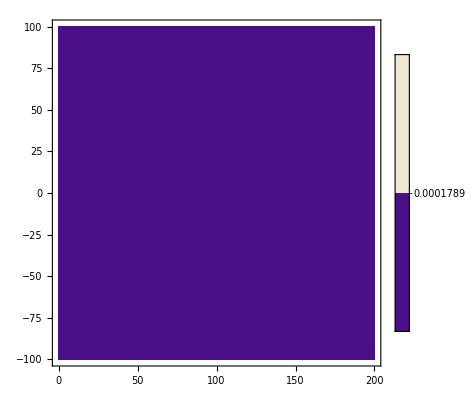

```mathematica
(* Plot convergence as function of dt*xi for k=2,4,8,16,64, with *different* RK schemes *)
butcher = GetButcher["Radau",5,"A",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",1,"L",2,1];
Ac=butcherC[[1]];
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
axislim = 100;
k=25;
pf=ContourPlot[phiFdiff[x+ⅈ y ,k,Af,bf,Ac,bc],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,1.0},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->10 ,PlotRangePadding->0];Show[pf]
```

```mathematica
phiFdiff[0.025+ⅈ 0.0 ,k,Af,bf,Ac,bc,1.0]
```

0.285081

```mathematica
(* Plot preconditioning of stage matrix \Phi for one RK scheme with a different.
This is *not* MGRIT convergence. *)
butcher = GetButcher["Radau",3,"A",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",4,"L",3,1];
Ac=butcherC[[1]];
(*Ac= {{Af[[1,1]],0,0},{Af[[2,1]],Af[[2,2]],0},{Af[[3,1]],Af[[3,2]],Af[[3,3]]}};*)
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
Eigenvalues[Inverse[Ac].Af]
axislim = 10;
zlim = 2.0;
pf1=ContourPlot[prec[x+ⅈ y ,Af,Ac][[1]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf2=ContourPlot[prec[x+ⅈ y ,Af,Ac][[2]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf3=ContourPlot[prec[x+ⅈ y ,Af,Ac][[3]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
Show[pf1]
Show[pf2]
Show[pf3]
```

(0.416667 | -0.0833333
0.75 | 0.25)

(0.25 | 0 | 0 | 0 | 0
0.5 | 0.25 | 0 | 0 | 0
0.34 | -0.04 | 0.25 | 0 | 0
0.272794 | -0.0503676 | 0.0275735 | 0.25 | 0
1.04167 | -1.02083 | 7.8125 | -7.08333 | 0.25)

Dot::dotsh: Tensors {{4.,0.,0.,0.,0.},{-8.,4.,4.32072×10^-16,1.6694×10^-15,-1.32146×10^-16},{-6.72,0.64,«19»,«24»,-8.63309×10^-17},{-5.23529,0.735294,-0.441176,4.,-4.21702×10^-17},{12.3333,17.1667,-137.5,113.333,4.}} and {{0.416667,-0.0833333},{0.75,0.25}} have incompatible shapes.

Eigenvalues[{{4.,0.,0.,0.,0.},{-8.,4.,4.32072×10^-16,1.6694×10^-15,-1.32146×10^-16},{-6.72,0.64,4.,1.57399×10^-15,-8.63309×10^-17},{-5.23529,0.735294,-0.441176,4.,-4.21702×10^-17},{12.3333,17.1667,-137.5,113.333,4.}}.{{0.416667,-0.0833333},{0.75,0.25}}]

Dot::dotsh: Tensors {{0.137951+0.344828 ⅈ,4.58972×10^-17+6.20779×10^-18 ⅈ,1.65775×10^-16+7.77803×10^-17 ⅈ,-8.07732×10^-18+1.0306×10^-16 ⅈ,-6.26605×10^-19+2.36809×10^-18 ⅈ},«3»,{1.10586-0.634062 ⅈ,«3»,0.137951+0.344828 ⅈ}} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Dot::dotsh: Tensors {«1»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«4»} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

Dot::dotsh: Tensors {{0.137951+0.344828 ⅈ,4.58972×10^-17+6.20779×10^-18 ⅈ,1.65775×10^-16+7.77803×10^-17 ⅈ,-8.07732×10^-18+1.0306×10^-16 ⅈ,-6.26605×10^-19+2.36809×10^-18 ⅈ},«3»,{1.10586-0.634062 ⅈ,«3»,0.137951+0.344828 ⅈ}} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 2 of Abs[Eigenvalues[{{0.137951+0.344828 ⅈ,4.58972×10^-17+6.20779×10^-18 ⅈ,1.65775×10^-16+7.77803×10^-17 ⅈ,-8.07732×10^-18+1.0306×10^-16 ⅈ,-6.26605×10^-19+2.36809×10^-18 ⅈ},«4»}.{{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},«1»}]] does not exist.

Dot::dotsh: Tensors {«1»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 2 of Abs[Eigenvalues[«1»]] does not exist.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«4»} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 2 of Abs[Eigenvalues[{{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,1.02928+0.987204 ⅈ,«1»,«18»+«1»,0.156397+0.324681 ⅈ}}.«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

Dot::dotsh: Tensors {{0.137951+0.344828 ⅈ,4.58972×10^-17+6.20779×10^-18 ⅈ,1.65775×10^-16+7.77803×10^-17 ⅈ,-8.07732×10^-18+1.0306×10^-16 ⅈ,-6.26605×10^-19+2.36809×10^-18 ⅈ},«3»,{1.10586-0.634062 ⅈ,«3»,0.137951+0.344828 ⅈ}} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 3 of Abs[Eigenvalues[{{0.137951+0.344828 ⅈ,4.58972×10^-17+6.20779×10^-18 ⅈ,1.65775×10^-16+7.77803×10^-17 ⅈ,-8.07732×10^-18+1.0306×10^-16 ⅈ,-6.26605×10^-19+2.36809×10^-18 ⅈ},«4»}.{{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},«1»}]] does not exist.

Dot::dotsh: Tensors {«1»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 3 of Abs[Eigenvalues[«1»]] does not exist.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«4»} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 3 of Abs[Eigenvalues[{{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,1.02928+0.987204 ⅈ,«1»,«18»+«1»,0.156397+0.324681 ⅈ}}.«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

SetPrecision::precsm: Requested precision 15.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*butcher = GetButcher["SDIRK",6,"L",3,1];*)
butcher = GetButcher["Radau",9,"A",3,1];
A=butcher[[1]];
b=butcher[[2]];
invA = Inverse[A];
(* Print high accuracy numbers *)
(*{NumberForm[A,18],
NumberForm[b, 18],
NumberForm[Total[A,{2}],18],
NumberForm[Inverse[A],18],
NumberForm[Eigenvalues[Inverse[A]],18],
NumberForm[b.Inverse[A],18]}*)

A //MatrixForm
{Q,R} = SchurDecomposition[invA];
(*dL ={{L1,0,0,0,0},{0,L2,0,0,0},{0,0,L3,0,0},{0,0,0,L4,0},{0,0,0,0,L5}};*)
dL ={{L1,0,0,0},{0,L2,0,0},{0,0,L3,0},{0,0,0,L4}};
(*dL ={{L1,0,0},{0,L2,0},{0,0,L3}};*)
(*dL ={{L1,0},{0,L2}};*)
(*Map[MatrixForm, SchurDecomposition[invA]]
NumberForm[Chop[Transpose[Q].dL.Q] //MatrixForm,2]*)
invA //MatrixForm
(Im[Eigenvalues[A]]/Re[Eigenvalues[A]])^2
(Im[Eigenvalues[invA]]/Re[Eigenvalues[invA]])^2
b.invA//MatrixForm

(*Test lower triangular preconditioning of Butcher *)
(*L = LowerTriangularize[A];
L.A //MatrixForm
Eigenvalues[L.A] //MatrixForm*)
```

(0.07299886431790332 | -0.02673533110794557 | 0.01867692976398435 | -0.01287910609330644 | 0.005042839233882015
0.1537752314791825 | 0.1462148678474935 | -0.03644456890512809 | 0.02123306311930472 | -0.007935579902728778
0.1400630456848099 | 0.2989671294912835 | 0.167585070135249 | -0.03396910168661775 | 0.01094428874419225
0.1448943081095348 | 0.2765000687601592 | 0.325797922910421 | 0.1287567532549098 | -0.01570891737880533
0.1437135607912259 | 0.2813560151494621 | 0.3118265229757413 | 0.2231039010835707 | 0.04)

(8.755923977938362 | 2.891942615380117 | -0.875186396200265 | 0.3997052079399655 | -0.1337061638492158
-7.161380720145387 | 1.806077724083644 | 2.363797176068608 | -0.8659007802831345 | 0.2743380777751942
4.122165246243374 | -4.496017125813395 | 0.8567652453971776 | 2.518320949211064 | -0.6570627571343601
-3.87866321972401 | 3.393151918064954 | -5.188340906407187 | 0.5812330525808164 | 2.809983655279712
8.412424223594289 | -6.970256116656661 | 8.777114204150473 | -18.2192823110881 | 13.)

{0,0.3170932253764324,0.3170932253764324,3.20414314469163,3.20414314469163}

{3.20414314469163,3.20414314469163,0.3170932253764324,0.3170932253764324,0}

(8.816207631167156×10^-39 | -8.816207631167156×10^-39 | -2.938735877055719×10^-39 | 1.175494350822288×10^-38 | 1.)

```mathematica
0.06941899716778033
```

```mathematica
(* Column sums of adjugate matrix *)
s = Flatten[Dimensions[Transpose[b],1]][[1]];
sc = ConstantArray[0,{1,s}];
sc[[1,s]]=1;
(* Stiffly accurate *)
(*NumberForm[sc.{{"[◼]", "Adjugate"}}[A - xx*IdentityMatrix[Length[A]]],20]*)
(* Non stiffly accurate *)
NumberForm[Simplify[(b.Inverse[A]).{{"[◼]", "Adjugate"}}[A - xx*IdentityMatrix[Length[A]]]],20]
```

{{-0.30947817319669026360+2.5955142953401056854 xx-4.6354730351246558152 xx^2,-0.045852128962388283706+0.010778510083830894926 xx+0.86733186872122709904 xx^2,0.11439002800791893735-0.95579390388301625604 xx+2.4671433633215880676 xx^2}}

```mathematica
(* Determinants and adjugates *)
ResourceFunction["Adjugate"]
M2 = {{m11-x,m12},{m21,m22-y}};
M2c = {{m11-xx,m12},{m21,m22-xx}};
A2 = {{m11,m12},{m21,m22}};
M3 = {{m11-xx,m12,m13},{m21,m22-yy,m23},{m31,m32,m33-zz}};
M3c = {{m11-xx,m12,m13},{m21,m22-xx,m23},{m31,m32,m33-xx}};
A3 = {{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}};
M4 = {{m11-xx,m12,m13,m14},{m21,m22-yy,m23,m24},{m31,m32,m33-zz,m34},{m41,m42,m43,m44-qq}};
M4c = {{m11-xx,m12,m13,m14},{m21,m22-xx,m23,m24},{m31,m32,m33-xx,m34},{m41,m42,m43,m44-xx}};
A4 = {{m11,m12,m13,m14},{m21,m22,m23,m24},{m31,m32,m33,m34},{m41,m42,m43,m44}};
M5c = {{m11-xx,m12,m13,m14,m15},{m21,m22-xx,m23,m24,m25},{m31,m32,m33-xx,m34,m35},{m41,m42,m43,m44-xx,m45},{m51,m52,m53,m54,m55-xx}};
A5 = {{m11,m12,m13,m14,m15},{m21,m22,m23,m24,m25},{m31,m32,m33,m34,m35},{m41,m42,m43,m44,m45},{m51,m52,m53,m54,m55}};
bb2 = {{b1,b2}}.A2;
bb3 = {{b1,b2,b3}}.A3;
bb4 = {{b1,b2,b3,b4}}.A4;
bb5 = {{b1,b2,b3,b4,b5}}.A5;
bsa2 = {{0,1}};
bsa3 = {{0,0,1}};
bsa4 = {{0,0,0,1}};
bsa5 = {{0,0,0,0,1}};
```

[◼] | Adjugate

```mathematica
Expand[bsa2.({{"[◼]", "Adjugate"}}[M2c])];
Expand[bsa3.({{"[◼]", "Adjugate"}}[M3c])];
Expand[bsa4.({{"[◼]", "Adjugate"}}[M4c])];
Expand[bsa5.({{"[◼]", "Adjugate"}}[M5c])];
Expand[bb2.({{"[◼]", "Adjugate"}}[M2c])];
Expand[bb3.({{"[◼]", "Adjugate"}}[M3c])];
Expand[bb4.({{"[◼]", "Adjugate"}}[M4c])];

{{"[◼]", "Adjugate"}}
```

```mathematica
{{"[◼]", "Adjugate"}}[A3]
Det[A4]
```

{{-m23 m32+m22 m33,m13 m32-m12 m33,-m13 m22+m12 m23},{m23 m31-m21 m33,-m13 m31+m11 m33,m13 m21-m11 m23},{-m22 m31+m21 m32,m12 m31-m11 m32,-m12 m21+m11 m22}}

m14 m23 m32 m41-m13 m24 m32 m41-m14 m22 m33 m41+m12 m24 m33 m41+m13 m22 m34 m41-m12 m23 m34 m41-m14 m23 m31 m42+m13 m24 m31 m42+m14 m21 m33 m42-m11 m24 m33 m42-m13 m21 m34 m42+m11 m23 m34 m42+m14 m22 m31 m43-m12 m24 m31 m43-m14 m21 m32 m43+m11 m24 m32 m43+m12 m21 m34 m43-m11 m22 m34 m43-m13 m22 m31 m44+m12 m23 m31 m44+m13 m21 m32 m44-m11 m23 m32 m44-m12 m21 m33 m44+m11 m22 m33 m44

```mathematica
nn = 4;
c0 = cG[nn];
D[x^nn*(x-1)^nn,{x,nn}]
```

24 (-1+x)^4+384 (-1+x)^3 x+864 (-1+x)^2 x^2+384 (-1+x) x^3+24 x^4

```mathematica
d4[x_]:=24 (-1+x)^4+384 (-1+x)^3 x+864 (-1+x)^2 x^2+384 (-1+x) x^3+24 x^4;
d4[c0[[4]]]
```

1.36209358401824669685969274009139359378×10^-55